```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol "MaTeX" appears in multiple contexts {"MaTeX`", "Global`"}; definitions in context "MaTeX`" may shadow or be shadowed by other definitions.

```mathematica
ConfigureMaTeX[]
```

{CacheSize→100,Ghostscript→/home/cplumber/bin/gs,pdfLaTeX→/local/site/pkg/texlive/2013/bin/x86_64-linux/pdflatex}

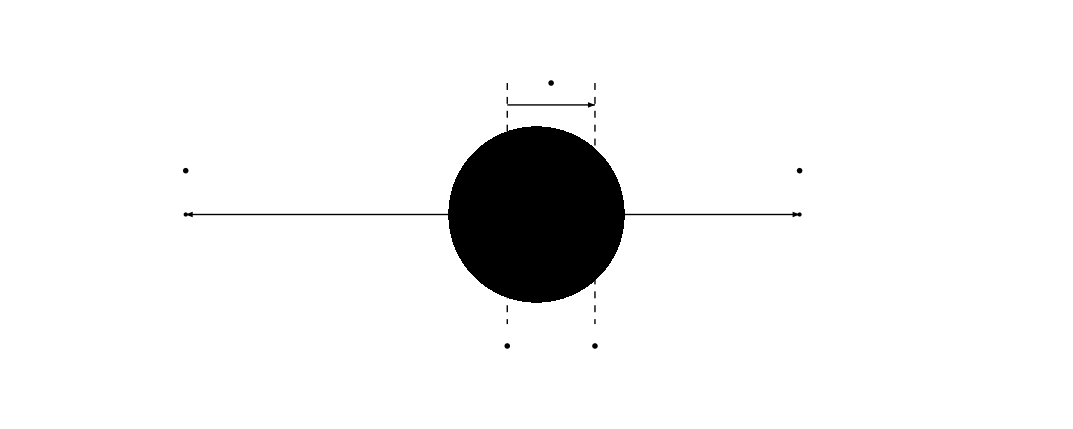

```mathematica
(*Colored noise, opposite directions*)
{p1,p2,p3,p4}={{-4,0},{-1/3,0},{2/3,0},{3,0}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)]/.R->1,{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\sim\\tau_C",Magnification->2],24],1/2(p2+p3)+{0,3/2}],Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2-{0,3/2})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,3/2})],{Thick,Arrowheads[{-2*10^-2,2*10^-2}],Arrow[{p2+{0,5/4},p3+{0,5/4}}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]},{Dashed,Line[{p3+{0,3/2},p3-{0,5/4}}]},{Dashed,Line[{p2+{0,3/2},p2-{0,5/4}}]}}}]]
```

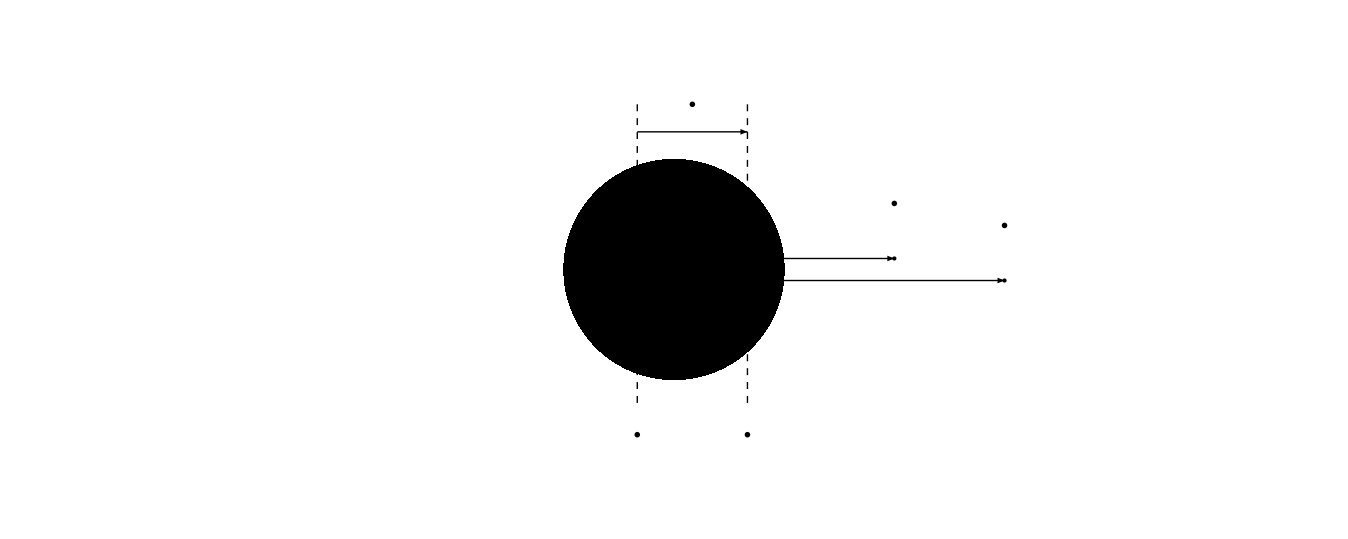

```mathematica
(*Colored noise, same direction*)
{offξ1,offξ2}={1/10,-1/10};
{p1,p2,p3,p4}={{2,offξ1},{-1/3,offξ1},{2/3,offξ2},{3,offξ2}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)]/.R->1,{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\sim\\tau_C",Magnification->2],24],1/2(p2+p3)+{0,3/2}],Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2-{0,3/2+offξ1})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,3/2+offξ2})],{Thick,Arrowheads[{-2*10^-2,2*10^-2}],Arrow[{p2+{0,5/4-offξ1},p3+{0,5/4-offξ2}}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]},{Dashed,Line[{p3+{0,3/2+offξ1},p3-{0,5/4-offξ1}}]},{Dashed,Line[{p2+{0,3/2+offξ2},p2-{0,5/4-offξ2}}]}}}]]
```

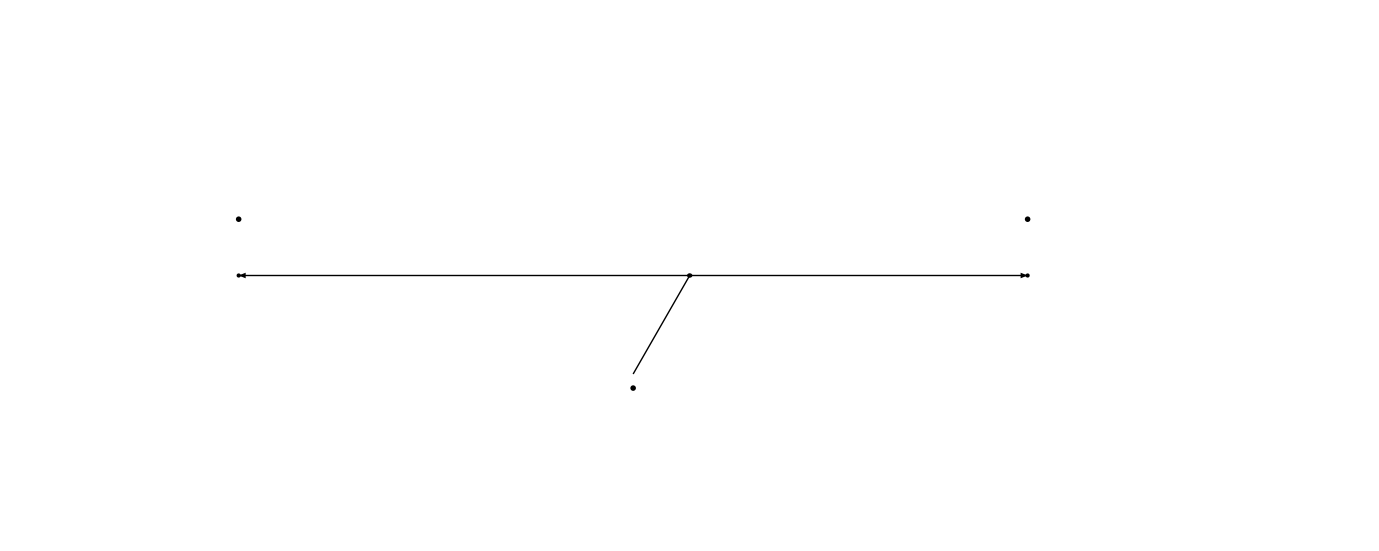

```mathematica
(*White noise, opposite directions*)
R=10^-2;
{p1,p2,p3,p4}={{-4,0},{-R/3,0},{(2R)/3,0},{3,0}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)],{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2})],Text[Style[MaTeX["\\tau_1=\\tau_2",Magnification->2],24],(1/2(p1+p4)-{0,1})],{Line[{1/2(p1+p4)-{0,7/8},1/2(p2+p3)}]},{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]}}}]]
```

```mathematica
(*White noise, same direction*)
R=10^-2;
{offξ1,offξ2}={1/10,-1/10};
{p1,p2,p3,p4}={{2,offξ1},{-R/3,offξ1},{(2R)/3,offξ2},{3,offξ2}};
Show[DensityPlot[√(R^2-(x^2+y^2))Exp[-((x^2+y^2)/R^2)^(1/2)],{x,-5,5},{y,-2,2},PlotPoints->250,ColorFunction->(Hue[0.5,0.5,0,#1]&),Frame->False,AspectRatio->Automatic],
Graphics[{Text[Style[MaTeX["\\xi_1",Magnification->2],24],(p1+{0,1/2})],Text[Style[MaTeX["\\xi_2",Magnification->2],24],(p4+{0,1/2-offξ2+offξ1})],Text[Style[MaTeX["\\tau_1",Magnification->2],24],(p2+{0,1/2+0offξ1})],Text[Style[MaTeX["\\tau_2",Magnification->2],24],(p3-{0,1/2+0offξ2})],{Arrowheads[{{0.02,2/3}}],Arrow[{p2,p1}]},{PointSize[Large],Point[{p1,p4,p2,p3}],{Arrowheads[{{0.02,2/3}}],Arrow[{p3,p4}]}}}]]
```

-Graphics-

```mathematica
1/τf^2 Integrate[2DQ (χQi Ti si^2)/τp^3 k^2 Exp[2DQ k^2(1/τf-1/τp)],{τp,τ0,τf},Assumptions->DQ>0&&0<τ0<τf&&k∈Reals]//FullSimplify
```

(si^2 Ti (-ⅇ^((2 DQ k^2 (τ0-τf))/(τ0 τf)) (2 DQ k^2+τ0) τf+τ0 (2 DQ k^2+τf)) χQi)/(2 DQ k^2 τ0 τf^3)

```mathematica
Out[148]/.{DQ->1/6,τ0->1/2,τf->8}
```

(3 (-8 ⅇ^(-(5 k^2)/8) (1/2+k^2/3)+1/2 (8+k^2/3)) si^2 Ti χQi)/(256 k^2)

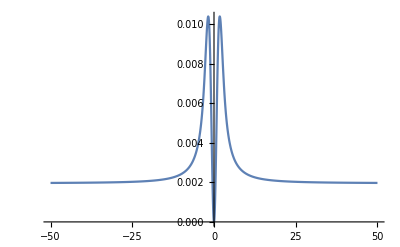

```mathematica
Plot[(3 (-8 ⅇ^(-(5 k^2)/8) (1/2+k^2/3)+1/2 (8+k^2/3)))/(256 k^2),{k,-50,50},PlotRange->All]
```

```mathematica
Limit[1/τf+1/(2DQ k^2)-(1/τ0+1/(2DQ k^2))Exp[-2DQ k^2(1/τ0-1/τf)],k->∞,Assumptions->DQ>0&&0<τ0<τf]
Limit[1/τf+1/(2DQ k^2)-(1/τ0+1/(2DQ k^2))Exp[-2DQ k^2(1/τ0-1/τf)],k->0,Assumptions->DQ>0&&0<τ0<τf]
```

1/τf

0

```mathematica
1/τf^2 Integrate[2DQ (χQi Ti si^2)/τp^1 k^2 Exp[2DQ k^2(1/τf-1/τp)],{τp,τ0,τf},Assumptions->DQ>0&&0<τ0<τf&&k>0]//FullSimplify
```

(2 DQ ⅇ^((2 DQ k^2)/τf) k^2 si^2 Ti χQi (ExpIntegralEi[-(2 DQ k^2)/τ0]-ExpIntegralEi[-(2 DQ k^2)/τf]))/τf^2

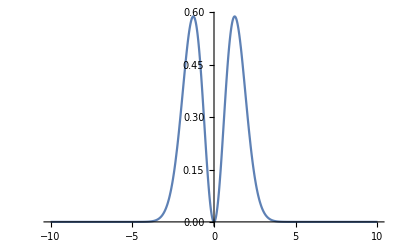

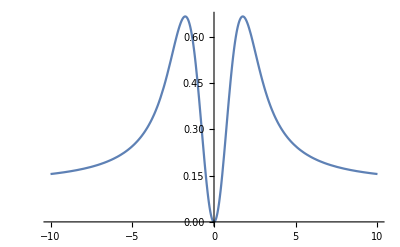

```mathematica
Plot[k^2 Exp[-2DQ k^2(1/τ0-1/τf)]/.{DQ->1/6,τ0->1/2,τf->8},{k,-10,10}]
Plot[1/τf+1/(2DQ k^2)-(1/τ0+1/(2DQ k^2))Exp[-2DQ k^2(1/τ0-1/τf)]/.{DQ->1/6,τ0->1/2,τf->8},{k,-10,10}]
```

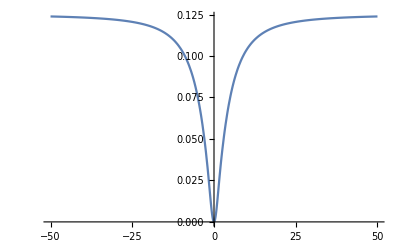

```mathematica
Plot[1/192 ⅇ^(k^2/24) k^2 (ExpIntegralEi[-(2 k^2)/3]-ExpIntegralEi[-k^2/24]),{k,-50,50},PlotRange->All]
```

```mathematica
1/τf^2 Integrate[2DQ (χQi Ti si^2)/τp^3 k^2 Exp[2DQ k^2(1/τf-1/τp)],{τp,τ0,τf},Assumptions->DQ>0&&0<τ0<τf&&k∈Reals]-(si^2 Ti χQi)/τf^3//FullSimplify
```

(si^2 Ti (τ0-ⅇ^((2 DQ k^2 (τ0-τf))/(τ0 τf)) (2 DQ k^2+τ0)) χQi)/(2 DQ k^2 τ0 τf^2)

((2^(1+1/6 (9-√(9-12 k^2))) k^2 Hypergeometric0F1[1/6 (6+√(9-12 k^2)),1/64] Hypergeometric1F1[3/2-√(1/4-k^2/3),1-2 √(1/4-k^2/3),1])/(ⅇ^(5/4) (3+√(9-12 k^2)))+(2^(-1+1/6 (9+√(9-12 k^2))) ((4 k^2+5 (3+√(9-12 k^2))) Hypergeometric1F1[1/6 (9-√(9-12 k^2)),3-1/2 √(1-(4 k^2)/3),1/2]+9 Hypergeometric1F1[1/6 (9-√(9-12 k^2)),4-1/2 √(1-(4 k^2)/3),1/2]) Hypergeometric1F1[3/2+√(1/4-k^2/3),1+2 √(1/4-k^2/3),1])/(ⅇ^(3/2) (-18+√(9-12 k^2))))/((2^(3/2+√(1/4-k^2/3)+1/6 (9-√(9-12 k^2))) k^2 Hypergeometric0F1[1/6 (6+√(9-12 k^2)),1/64] Hypergeometric1F1[3/2-√(1/4-k^2/3),1-2 √(1/4-k^2/3),1/2])/(ⅇ^(3/4) (3+√(9-12 k^2)))+(2^(-1/2-√(1/4-k^2/3)+1/6 (9+√(9-12 k^2))) ((4 k^2+5 (3+√(9-12 k^2))) Hypergeometric1F1[1/6 (9-√(9-12 k^2)),3-1/2 √(1-(4 k^2)/3),1/2]+9 Hypergeometric1F1[1/6 (9-√(9-12 k^2)),4-1/2 √(1-(4 k^2)/3),1/2]) Hypergeometric1F1[3/2+√(1/4-k^2/3),1+2 √(1/4-k^2/3),1/2])/(ⅇ (-18+√(9-12 k^2))))

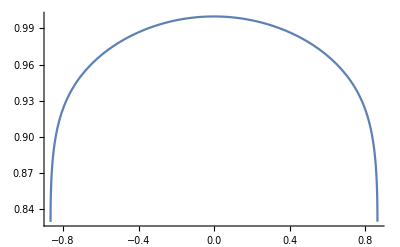

```mathematica
λ[k_]:=√(1/4-k^2/3);
ψp[k_,x_]:=x^(λ[k]-1/2)E^-x Hypergeometric1F1[λ[k]+3/2,2λ[k]+1,x];
ψm[k_,x_]:=x^(-λ[k]-1/2)E^-x Hypergeometric1F1[-λ[k]+3/2,-2λ[k]+1,x];
Dψp[k_,x_]:=-(2 ⅇ^(-x/2) k^2 x^(1/6 (-9+√(9-12 k^2))) Hypergeometric0F1[1/6 (6+√(9-12 k^2)),x^2/16])/(3+√(9-12 k^2));
Dψm[k_,x_]:=(ⅇ^-x x^(1/6 (-9-√(9-12 k^2))) ((4 k^2+5 (3+√(9-12 k^2))) Hypergeometric1F1[1/6 (9-√(9-12 k^2)),3-1/2 √(1-(4 k^2)/3),x]+18 x Hypergeometric1F1[1/6 (9-√(9-12 k^2)),4-1/2 √(1-(4 k^2)/3),x]))/(2 (-18+√(9-12 k^2)));
(ψp[k,xf]Dψm[k,x]-ψm[k,xf]Dψp[k,x])/(ψp[k,x]Dψm[k,x]-ψm[k,x]Dψp[k,x])/.{xf->1,x->1/2}
Plot[%,{k,-3,3},AxesOrigin->{0,0},PlotRange->All,PlotPoints->200]
```

```mathematica
Solve[τδn''[τ]+(1/τQ+2/τ)τδn'[τ]+(vQ^2 k^2)/τ^2 τδn[τ]==0,τδn[τ]]
D[τδn''[τ]+(1/τQ+2/τ)τδn'[τ]+(vQ^2 k^2)/τ^2 τδn[τ],τ]/.%[[1]]//FullSimplify
```

{{τδn[τ]→-(τ (τ τδn'[τ]+2 τQ τδn'[τ]+τ τQ τδn''[τ]))/(k^2 vQ^2 τQ)}}

((2 τ+(2+k^2 vQ^2) τQ) τδn'[τ]+τ ((τ+4 τQ) τδn''[τ]+τ τQ τδn^(3)[τ]))/(τ^2 τQ)

```mathematica
CoefficientList[((2 τ+(2+k^2 vQ^2) τQ) τδn'[τ]+τ ((τ+4 τQ) τδn''[τ]+τ τQ Derivative[3][τδn][τ]))/(τ^2 τQ),{Derivative[3][τδn][τ],τδn''[τ],τδn'[τ]}]//Expand
```

{{{0,2/τ^2+(k^2 vQ^2)/τ^2+2/(τ τQ)},{4/τ+1/τQ,0}},{{1,0},{0,0}}}

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
Op[f_,τ_]:=D[f, τ];
rules={ψp''[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],ψm''[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τ^2 ψm[τp]}
morerules={Dψp''[τp]->-(1/τQ+4/τp)Dψp'[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))Dψp[τp],Dψm''[τp]->-(1/τQ+4/τp)Dψm'[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))Dψm[τp],Dψp'[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],Dψm'[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τp^2 ψm[τp],Dψp[τp]->ψp'[τp],Dψm[τp]->ψm'[τp]}
ap[τp_]:=(I k Dψm[τp])/(ψp[τp]Dψm[τp]-ψm[τp]Dψp[τp]);
am[τp_]:=(-I k Dψp[τp])/(ψp[τp]Dψm[τp]-ψm[τp]Dψp[τp]);
G[τ_,τp_]:=ap[τp]ψp[τ]+am[τp]ψm[τ];
(((-Dψp[τp] ψm[τp]+Dψm[τp] ψp[τp])Op[ap[τp],τp]//.rules)//.morerules)//FullSimplify
(((-Dψp[τp] ψm[τp]+Dψm[τp] ψp[τp])Op[am[τp],τp]//.rules)//.morerules)//FullSimplify
D[(((τp^2(-Dψp[τp] ψm[τp]+Dψm[τp] ψp[τp])Op[G[τ,τp],τp]//.rules)//.morerules)//FullSimplify), τp]/(-vQ^2 G[τ,τp](-Dψp[τp] ψm[τp]+Dψm[τp] ψp[τp])//.rules//.morerules)//FullSimplify
```

{ψp''[τp]→-(k^2 vQ^2 ψp[τp])/τp^2+(-2/τp-1/τQ) ψp'[τp],ψm''[τp]→-(k^2 vQ^2 ψm[τp])/τ^2+(-2/τp-1/τQ) ψm'[τp]}

{Dψp''[τp]→-(2/τp^2+(k^2 vQ^2)/τp^2+2/(τp τQ)) Dψp[τp]+(-4/τp-1/τQ) Dψp'[τp],Dψm''[τp]→-(2/τp^2+(k^2 vQ^2)/τp^2+2/(τp τQ)) Dψm[τp]+(-4/τp-1/τQ) Dψm'[τp],Dψp'[τp]→-(k^2 vQ^2 ψp[τp])/τp^2+(-2/τp-1/τQ) ψp'[τp],Dψm'[τp]→-(k^2 vQ^2 ψm[τp])/τp^2+(-2/τp-1/τQ) ψm'[τp],Dψp[τp]→ψp'[τp],Dψm[τp]→ψm'[τp]}

-(ⅈ k^3 vQ^2 ψm[τp])/τp^2

(ⅈ k^3 vQ^2 ψp[τp])/τp^2

k^2

(ⅈ (-k ψp[τ] ψm'[τp]+k ψm[τ] ψp'[τp]))/(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp])

```mathematica
I D[(((τp^2 (ψp[τ] ψm'[τp]-ψm[τ] ψp'[τp])Op[Log[G[τ,τp]],τp]//.rules)//.morerules)//FullSimplify), τp]/(vQ^2(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp])(G[τ,τp]//.morerules//FullSimplify))//FullSimplify
```

k

```mathematica
(*My claim: *)I D[(((τp^2 (ψp[τ] ψm'[τp]-ψm[τ] ψp'[τp])Op[Log[G[τ,τp]],τp]//.rules)//.morerules)//FullSimplify), τp]/(vQ^2(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp]))==k G[τ,τp]
```

(ⅈ (-k ψp[τ] ψm'[τp]+k ψm[τ] ψp'[τp]))/(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp])

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
Op[f_,τ_]:=D[f, τ];
rules={ψp''[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],ψm''[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τ^2 ψm[τp],Derivative[3][ψp][τp]->-(1/τQ+4/τp)ψp''[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))ψp'[τp],Derivative[3][ψm][τp]->-(1/τQ+4/τp)ψm''[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))ψm'[τp]};

ap[τp_]:=(I k ψm'[τp])/(ψp[τp]ψm'[τp]-ψm[τp]ψp'[τp]);
am[τp_]:=(-I k ψp'[τp])/(ψp[τp]ψm'[τp]-ψm[τp]ψp'[τp]);
G[τ_,τp_]:=ap[τp]ψp[τ]+am[τp]ψm[τ];
I D[(τp^2 (ψp[τ] ψm'[τp]-ψm[τ] ψp'[τp])Op[Log[G[τ,τp]],τp]), τp]/(vQ^2(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp]))//.rules//FullSimplify
```

(ⅈ k^2 (τ^2 ψp[τp] ψm'[τp]-τp^2 ψm[τp] ψp'[τp]) (ψp[τp] (k^2 vQ^2 (τ-τp) (τ+τp) ψm[τp] (-ψm[τp] ψp[τ]+ψm[τ] ψp[τp])+τ^2 τp^2 ψp[τ] ψm'[τp]^2)-τ^2 τp^2 (ψm[τp] ψp[τ]+ψm[τ] ψp[τp]) ψm'[τp] ψp'[τp]+τ^2 τp^2 ψm[τ] ψm[τp] ψp'[τp]^2))/(τ^4 τp^2 (ψp[τp] ψm'[τp]-ψm[τp] ψp'[τp])^3)

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
Op[f_,τ_]:=D[f, τ];
rules={ψp''[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],ψm''[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τ^2 ψm[τp],Derivative[3][ψp][τp]->-(1/τQ+4/τp)ψp''[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))ψp'[τp],Derivative[3][ψm][τp]->-(1/τQ+4/τp)ψm''[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))ψm'[τp]};

(I D[(τp^2 (ψp[τ] ψm'[τp]-ψm[τ] ψp'[τp])Op[Log[G[τ,τp]],τp]), τp]/(vQ^2(-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp]))/.{ψp[τ] ψm'[τp]-ψm[τ] ψp'[τp]->G[τ,τp]/(I k)(ψp[τp]ψm'[τp]-ψm[τp]ψp'[τp])})//.rules//FullSimplify
```

(G^(0,1)[τ,τp] (τp τQ ψm[τp] (ⅈ k^3 vQ^2 τp ψp[τ]+τ^2 ψp'[τp] (2 G[τ,τp]-τp G^(0,1)[τ,τp]))+τ^2 (-ⅈ k ψm[τ] (k^2 vQ^2 τQ ψp[τp]+τp (τp+2 τQ) ψp'[τp])+τp ψm'[τp] (ⅈ k (τp+2 τQ) ψp[τ]+τQ ψp[τp] (-2 G[τ,τp]+τp G^(0,1)[τ,τp]))))+τ^2 τp^2 τQ G[τ,τp] (-ψp[τp] ψm'[τp]+ψm[τp] ψp'[τp]) G^(0,2)[τ,τp])/(k vQ^2 τ^2 τQ G[τ,τp] (ψp[τp] ψm'[τp]-ψm[τp] ψp'[τp]))

```mathematica
(*YET ANOTHER ATTEMPT*)
ClearAll["Global`*"];
Remove["Global`*"];
Op[f_,τ_]:=D[f, τ];
rules={ψp''[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],ψm''[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τ^2 ψm[τp]};
morerules={Dψp''[τp]->-(1/τQ+4/τp)Dψp'[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))Dψp[τp],Dψm''[τp]->-(1/τQ+4/τp)Dψm'[τp]-((vQ^2 k^2)/τp^2+2/τp^2+2/(τp τQ))Dψm[τp],Dψp'[τp]->-(1/τQ+2/τp)ψp'[τp]-(vQ^2 k^2)/τp^2 ψp[τp],Dψm'[τp]->-(1/τQ+2/τp)ψm'[τp]-(vQ^2 k^2)/τp^2 ψm[τp],Dψp[τp]->ψp'[τp],Dψm[τp]->ψm'[τp]};
ap[τp_]:=(I k Dψm[τp])/(ψp[τp]Dψm[τp]-ψm[τp]Dψp[τp]);
am[τp_]:=(-I k Dψp[τp])/(ψp[τp]Dψm[τp]-ψm[τp]Dψp[τp]);
G[τ_,τp_]:=ap[τp]ψp[τ]+am[τp]ψm[τ];
((D[G[τ,τp], τp]//.rules)//.morerules)//FullSimplify
```

(ⅈ k^3 vQ^2 (-ψm[τp] ψp[τ]+ψm[τ] ψp[τp]))/(τp^2 (ψp[τp] ψm'[τp]-ψm[τp] ψp'[τp]))

```mathematica
DSolve[ρ''[x]+ρ'[x]+k^2 ρ[x]==0,ρ[x],x]
```

{{ρ[x]→ⅇ^(1/2 (-1-√(1-4 k^2)) x) C[1]+ⅇ^(1/2 (-1+√(1-4 k^2)) x) C[2]}}